```mathematica
choose[k_,n_]:=Module[{t,r},
t={};
While[Length[t]<k,
r={RandomInteger[{1,n}],RandomInteger[{1,n}]};
While[MemberQ[t,r],r={RandomInteger[{1,n}],RandomInteger[{1,n}]}];
AppendTo[t,r]];t]
```

```mathematica
d[{x_,y_}]:=(x-y).(x-y)
```

```mathematica
others[{{x1_,y1_},{x2_,y2_}}]:=Which[x1==x2,Table[{x1,y},{y,Min[y1,y2]+1,Max[y1,y2]-1}],
y1==y2,Table[{x,y1},{x,Min[x1,x2]+1,Max[x1,x2]-1}],True,temp=GCD[Abs[x2-x1],Abs[y2-y1]];Table[(t{x1,y1}+(temp-t){x2,y2})/temp,{t,1,temp-1}]]
```

```mathematica
check[L_]:=(Length[Union[Map[d,Partition[L,2,1]]]]==Length[L]-1)&&(Intersection[Union[L],Union[Flatten[Map[others,Partition[L,2,1]],1]]]=={})
```

```mathematica
pic1[L_]:=Module[{x,y},
x=Transpose[L][[1]];
y=Transpose[L][[2]];
xmin=Min[x];xmax=Max[x];
ymin=Min[y];ymax=Max[y];
Graphics[{Line[{{xmin-1/2,ymin-1/2},{xmax+1/2,ymin-1/2},{xmax+1/2,ymax+1/2},{xmin-1/2,ymax+1/2},{xmin-1/2,ymin-1/2}}],AbsolutePointSize[7],Map[Point,L]},PlotRange->{{xmin-1,xmax+1},{ymin-1,ymax+1}},ImageSize->20{xmax-xmin+2,ymax-ymin+2}]]
```

```mathematica
pic2[L_]:=Module[{x,y},
x=Transpose[L][[1]];
y=Transpose[L][[2]];
xmin=Min[x];xmax=Max[x];
ymin=Min[y];ymax=Max[y];
Graphics[{Line[{{xmin-1/2,ymin-1/2},{xmax+1/2,ymin-1/2},{xmax+1/2,ymax+1/2},{xmin-1/2,ymax+1/2},{xmin-1/2,ymin-1/2}}],Red,AbsoluteThickness[2],Line[L],Black,AbsolutePointSize[7],Map[Point,L]},PlotRange->{{xmin-1,xmax+1},{ymin-1,ymax+1}},ImageSize->20{xmax-xmin+2,ymax-ymin+2}]]
```

```mathematica
For[i=1,i>0,i++,
a=choose[8,4];L=Map[{First[a]}~Join~#~Join~{First[a]}&,Permutations[Rest[a]]];
s=Select[L,check];
If[Length[s]==2,Print[pic1[s[[1]]]];Print[pic2[s[[1]]]]]]
```

## 9 in 5x5

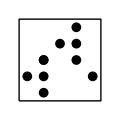

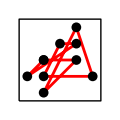

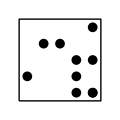

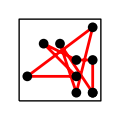

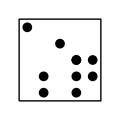

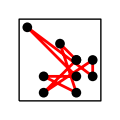

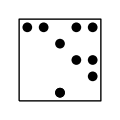

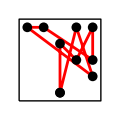

## 9 in 4x5

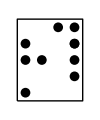

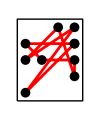

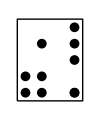

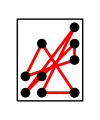

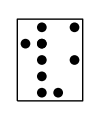

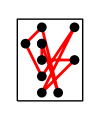

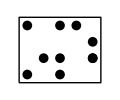

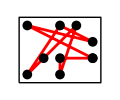

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

## 9 in 4x4

-Graphics-

-Graphics-

## 8 in 4x4

-Graphics-

-Graphics-

-Graphics-

«11 more identical outputs»

## 7 in 4x4

-Graphics-

-Graphics-

-Graphics-

«15 more identical outputs»

## 6 in 3x4

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»